# 4QFT on SiDelft

### Modules

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, plotglobalphase:False]. Calculate distance of 2 matrices by max_λ |(U-V)|, 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,plotglobalphase_:False]:=Module[{globalphase,mindist,F,ϕ},
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"}]];
{mindist,ϕ/.globalphase}
]
HSDistance::usage="HSDistance[ansatz,θvars,unitary,nqubits]";
HSDistance[ansatz_,θvars_,unitary_,nqubits_]:=Module[{ρ,ψ,f},
ρ=CreateDensityQureg[2*nqubits];
ψ=CreateQureg[2*nqubits];
ApplyCircuit[InitZeroState@ψ,bellpairs[nqubits]];
ApplyCircuit[InitZeroState@ρ,bellpairs[nqubits]];
ApplyCircuit[ρ,{Subscript[U, Sequence@@Range[0,nqubits-1]][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,ansatz/.θvars];
f=CalcFidelity[ρ,ψ];
DestroyQureg/@{ρ,ψ};
1-f
]
bellpairs::usage="create n-bell pairs";
bellpairs[n_,reverse_:False]:=With[{bp=Flatten[{Subscript[H, #1],Subscript[C, #1][Subscript[X, #2]]}&@@@Transpose@{Range[0,n-1],Range[n,2n-1]}]},If[reverse,Reverse@bp,bp]]
checkedConfψ[nqubit_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
conf=DefaultConfig[nqubit,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStatesψ[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

checkedConfρ[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

varMeanInitStatesψ::usage="varMeanInitStates[conf]. Calculate mean and variance of initial random states applied to the unitary.";
varMeanInitStatesψ[conf_]:=Module[{weights,ψwork,ψ,vm,g},
ψwork=CreateQureg[conf["nqubit"]];
ψ=CreateQureg[conf["nqubit"]];
vm=Association[
Table[
CloneQureg[ψ,conf["ψinit"][k]];
ApplyCircuit[ψ,conf["undocirc"][k]];
g=Calc2QubitCorr[conf["nqubit"],ψ,ψwork];
weights=PropertyValue[g,EdgeWeight];
k->{Mean[weights],Variance[weights]}
,{k,Keys@conf["ψinit"]}]];
DestroyQureg[ψwork];
DestroyQureg[ψ];
vm
]
```

### Definition of ansatze and sanity check

```mathematica
ansatz={Subscript[Rx, 0][Subscript[θ, 120]],Subscript[Ry, 3][Subscript[θ, 56]],Subscript[Ry, 0][Subscript[θ, 123]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 59]]],Subscript[Rx, 0][Subscript[θ, 124]],Subscript[SWAP, 1,2],Subscript[Ry, 1][Subscript[θ, 42]],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 50]]],Subscript[Ry, 0][Subscript[θ, 7]],Subscript[C, 1][Subscript[Ph, 2][Subscript[θ, 33]]],Subscript[Rx, 0][Subscript[θ, 17]],Subscript[SWAP, 2,3],Subscript[Rx, 1][Subscript[θ, 9]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 11]]],Subscript[SWAP, 2,3],Subscript[Rx, 3][Subscript[θ, 15]],Subscript[Ry, 2][Subscript[θ, 68]],Subscript[Ry, 3][Subscript[θ, 16]],Subscript[Rx, 2][Subscript[θ, 69]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 97]]],Subscript[SWAP, 1,2],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 103]]],Subscript[Ry, 0][Subscript[θ, 104]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3]};
θvars=<|Subscript[θ, 7]->3.1415553081326135,Subscript[θ, 9]->-3.1415902761443144,Subscript[θ, 11]->-5.497781449174974,Subscript[θ, 15]->3.141592396414565,Subscript[θ, 16]->3.141589972815106,Subscript[θ, 17]->-3.141586998968119,Subscript[θ, 33]->-1.5707929977286346,Subscript[θ, 42]->1.570798121323009,Subscript[θ, 50]->-0.7853987794252625,Subscript[θ, 56]->-1.5708008555616957,Subscript[θ, 59]->1.5707925829678986,Subscript[θ, 68]->1.570804921837841,Subscript[θ, 69]->-1.570796911567822,Subscript[θ, 97]->1.5707970860430527,Subscript[θ, 103]->0.3927006396217121,Subscript[θ, 104]->1.5707772216030695,Subscript[θ, 120]->-1.5707621567171606,Subscript[θ, 123]->0.7853977194886816,Subscript[θ, 124]->1.5707583339002782|>;
```

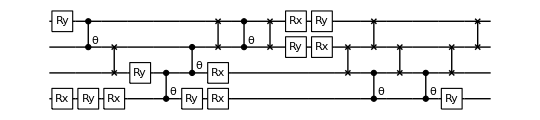

```mathematica
DrawCircuit[ansatz,4]
```

Distances given pristine qubits

```mathematica
unitary=CalcCircuitMatrix[DeleteCases[GetKnownCircuit["QFT",4],Subscript[SWAP, __]]];
```

```mathematica
MatrixDist[unitary,CalcCircuitMatrix[ansatz/.θvars]]
```

{0.0000172466,1.1781}

```mathematica
HSDistance[ansatz,θvars,unitary,4]
```

1.16544×10^-10

Use native gates, refine the search and check the new distance for sanity check

```mathematica
CustomGatesDefinitions
```

{SWAP_(p_,q_):>Sequence@@{Rx_p[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2]},PSW_(index1_,index2_)[θ_]:>U_(index1,index2)[{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2) Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],0},{0,-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],ⅇ^((ⅈ θ)/2) Cos[θ/2],0},{0,0,0,1}}]}

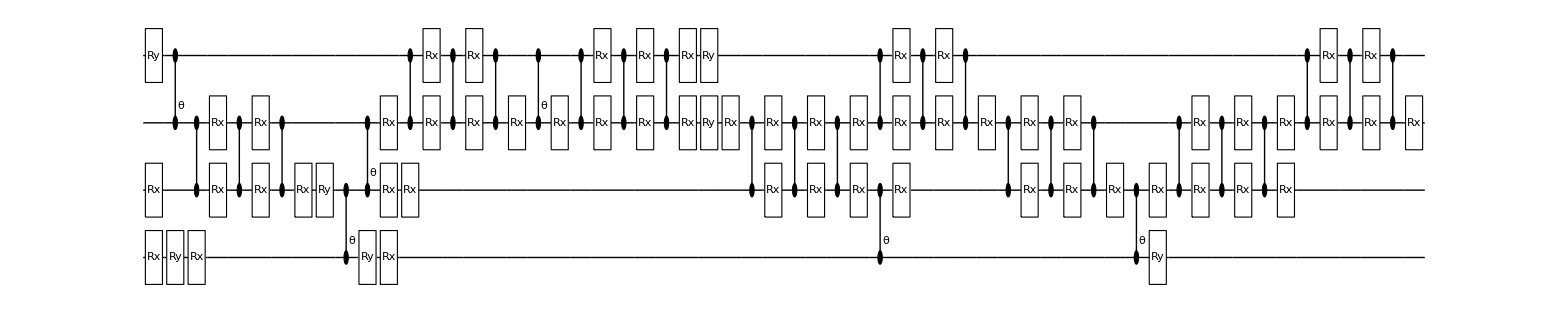

```mathematica
DrawCircuit[ansatz/.CustomGatesDefinitions,4]
```

```mathematica
HSDistance[ansatz/.CustomGatesDefinitions,θvars,unitary,4]
```

1.16544×10^-10

### Four qubits Silicon device

```mathematica
Options[SiliconDelft]={
qubitsNum->4,
T1->10^4,
T2-><|0-> 40.1,1-> 37.2,2-> 44.7,3-> 26.7|>,
QubitFreq-><|0-> 16.3*10^3,1-> 16.1*10^3,2-> 15.9*10^3,3-> 15.69*10^3|>,
RabiFreq-><|0->5,1->5,2->5,3->5|>,
OffResonantRabi->True,
StdPassiveNoise->True,
FidSingleXY-><|0-> 0.9996,1-> 0.9988,2-> 0.9991,3-> 0.9989|>,
EFSingleXY->{0,1},
FreqCZ-><|0-> 6.6,1-> 9.8,2-> 5.4|>,
FidCZ-><|0->0.9166807085341168,1->0.9805456134451412,2->0.9649648861853775|>,
EFCZ->{0,1},
ExchangeRotOn->{{0,0.07,0.042},{0.031,0,0.25},{0.02,0.03,0}},
ExchangeRotOff-><|0->0.03 ,1->0.02,2-> 0.028|>,
FidRead->0.99,
DurRead->10};
```

### Noisy fixed start with various gradients.

```mathematica
dev=SiliconDelft[];
confdef=checkedConfρ[dev,unitary,10,{0,1,2,3}];
```

```mathematica
grads={"NGAN","NGP","NGSTO","GPS","GPSTO","GCD","GCDSTO","GFD","GFDSTO"}
```

{NGAN,NGP,NGSTO,GPS,GPSTO,GCD,GCDSTO,GFD,GFDSTO}

```mathematica
ansatzdum={Subscript[Rx, 0][Subscript[θ, 0]],Subscript[Ry, 3][Subscript[θ, 1]],Subscript[Ry, 0][Subscript[θ, 2]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 3]]],Subscript[Rx, 0][Subscript[θ, 4]]};
θvarsdum=<|{ Subscript[θ, 0]->3.,Subscript[θ, 1]->-1,Subscript[θ, 2]->-5.497781449174974,Subscript[θ, 3]->3.141592396414565,Subscript[θ, 4]->3.141589972815106}|>;
```

```mathematica
results=<||>;
```

Compilation with predetermined ansatz using gradient methode NGAN @Wed 26 Oct 2022 00:02:18

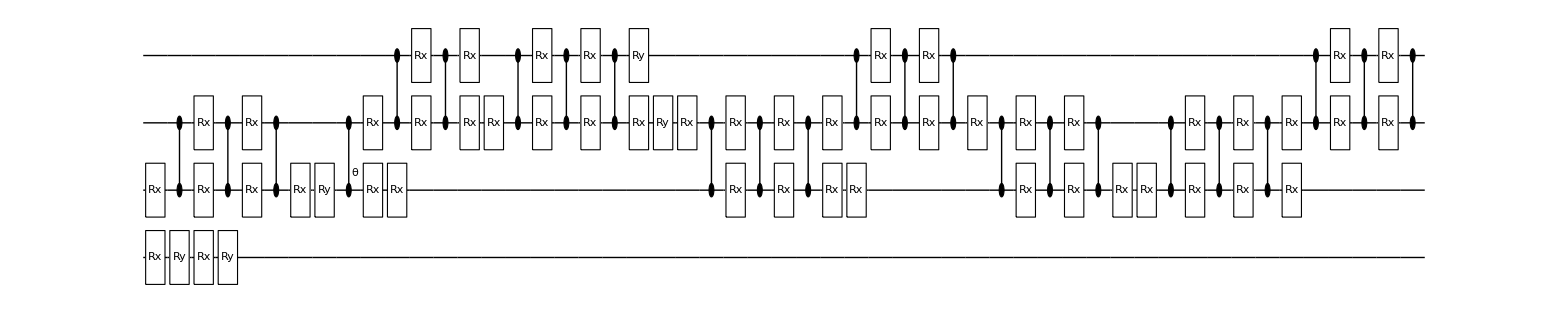
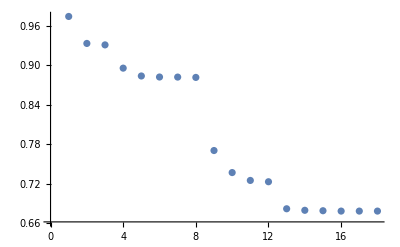
0.678343
320.598 min
-Graphics-
{Rx_0[θ_120],Rx_1[π/2],Ry_0[θ_123],C_1[Z_2],Rx_0[θ_124],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_3[π/2],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Ry_3[θ_16],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3]}
<|θ_7→4.54576,θ_9→-3.14848,θ_16→3.159,θ_33→-4.48699,θ_42→1.61533,θ_68→0.786292,θ_69→-2.11529,θ_120→-1.54062,θ_123→0.981729,θ_124→1.40255|>
-Graphics-

Compilation with predetermined ansatz using gradient methode NGP @Wed 26 Oct 2022 05:22:56

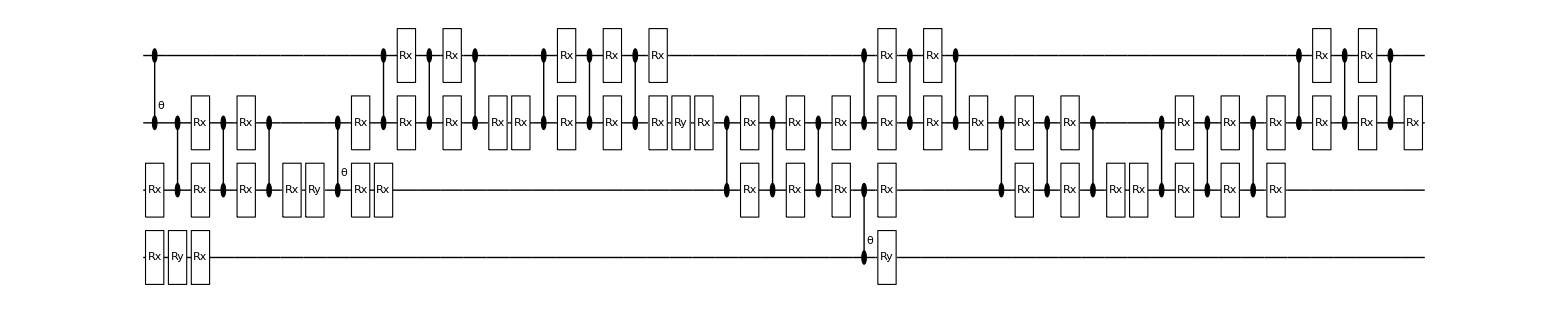
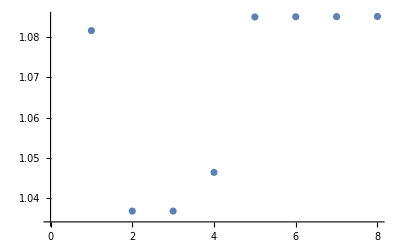
1.08505
16.7132 min
-Graphics-
{Rx_0[θ_120],Rx_1[π/2],C_2[Ph_3[θ_59]],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],Rx_0[θ_17],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],C_0[Ph_1[θ_97]],Rx_2[π/2],Rx_3[π/2],Rx_1[π/2],Ry_0[θ_104],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.13104,θ_9→-3.14252,θ_15→3.14141,θ_17→-3.12833,θ_33→-1.57362,θ_42→1.572,θ_59→1.57311,θ_68→1.55886,θ_69→-1.57649,θ_97→1.57216,θ_104→1.55812,θ_120→0.00271895|>
-Graphics-

Compilation with predetermined ansatz using gradient methode NGSTO @Wed 26 Oct 2022 05:39:39

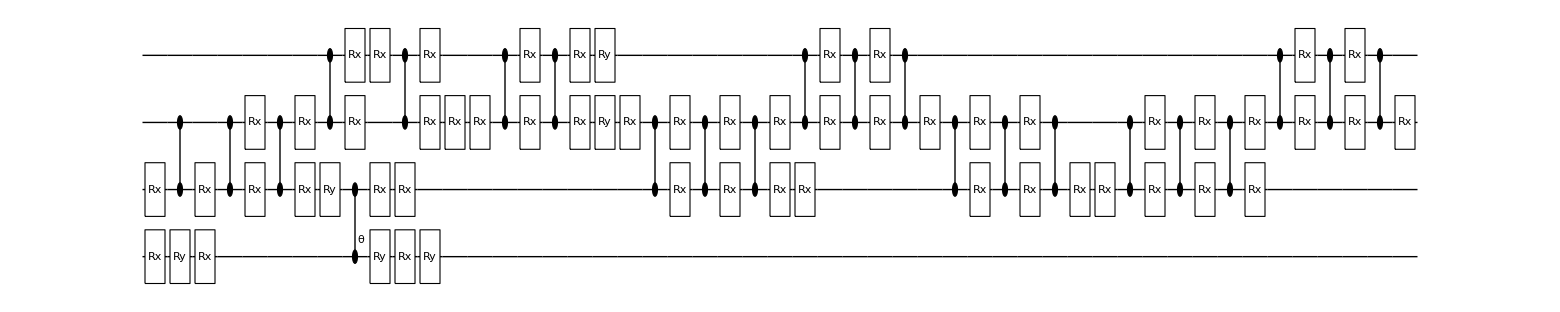
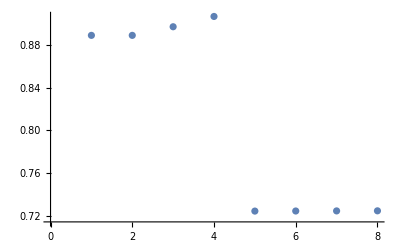
0.724857
173.188 min
-Graphics-
{Rx_0[θ_120],Rx_1[π/2],Ry_0[θ_123],C_1[Z_2],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],Ry_1[θ_42],C_2[Z_3],C_0[Ph_1[θ_50]],Rx_3[π/2],Rx_2[π/2],Ry_0[θ_7],Rx_1[θ_9],Rx_3[π/2],Rx_0[θ_17],Rx_1[π/2],C_2[Z_3],Ry_0[θ_104],Rx_2[π/2],Rx_3[π/2],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.1612,θ_9→-3.14206,θ_15→3.13864,θ_16→3.1401,θ_17→-3.13031,θ_42→1.57252,θ_50→-0.793309,θ_68→1.57082,θ_69→-1.57092,θ_104→1.56854,θ_120→-1.57497,θ_123→0.797264,θ_124→1.55904|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GPS @Wed 26 Oct 2022 08:32:50

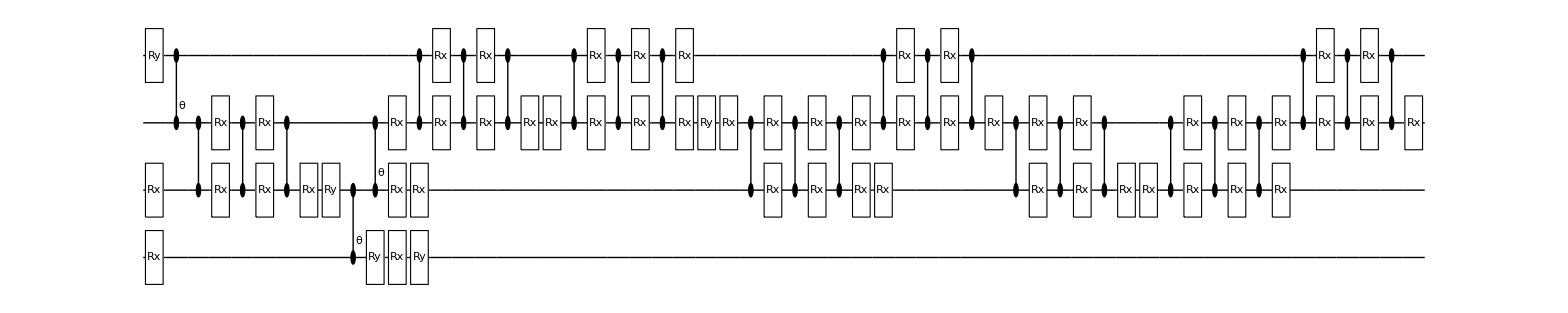
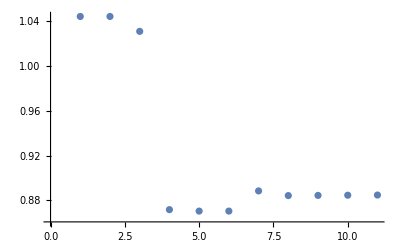
0.884363
117.559 min
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],C_2[Ph_3[θ_59]],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Ry_0[θ_104],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.13893,θ_9→-3.14734,θ_15→3.14411,θ_17→-3.13554,θ_33→-1.56289,θ_42→1.56915,θ_50→-0.776023,θ_56→-1.5639,θ_59→1.56364,θ_68→1.56261,θ_69→-1.55498,θ_104→1.56231,θ_120→-0.0148919|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GPSTO @Wed 26 Oct 2022 10:30:24

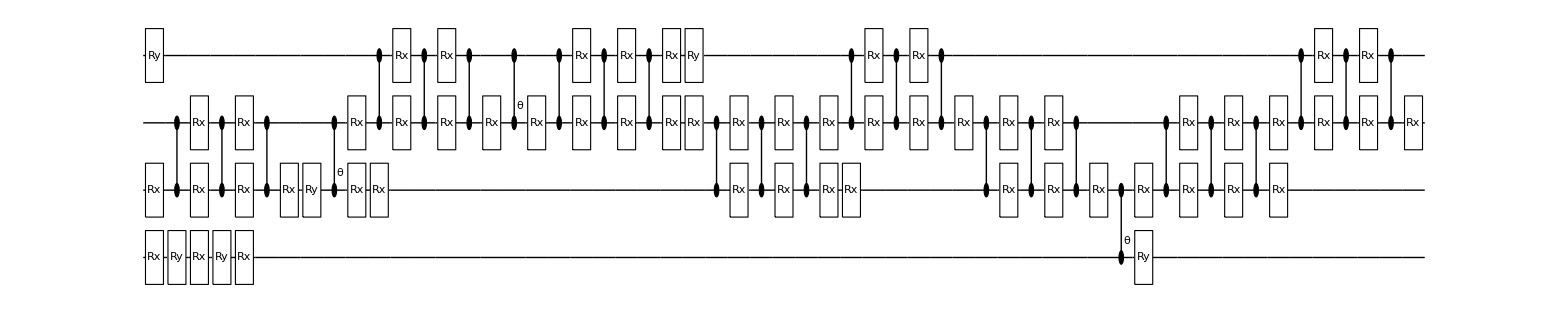
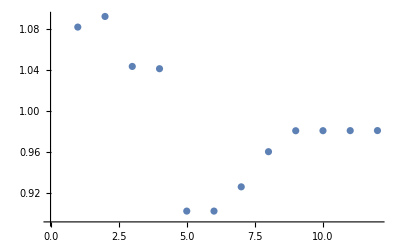
0.980956
174.878 min
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],Ry_0[θ_123],C_1[Z_2],Rx_0[θ_124],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],Rx_0[θ_17],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_3[θ_16],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14719,θ_9→-3.13874,θ_11→-5.4956,θ_15→3.14153,θ_16→3.14344,θ_17→-3.13635,θ_33→-1.57656,θ_42→1.57339,θ_56→-1.57352,θ_69→-1.5611,θ_103→0.397191,θ_104→1.56551,θ_120→-1.58098,θ_123→0.783329,θ_124→1.56887|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GCD @Wed 26 Oct 2022 13:25:16

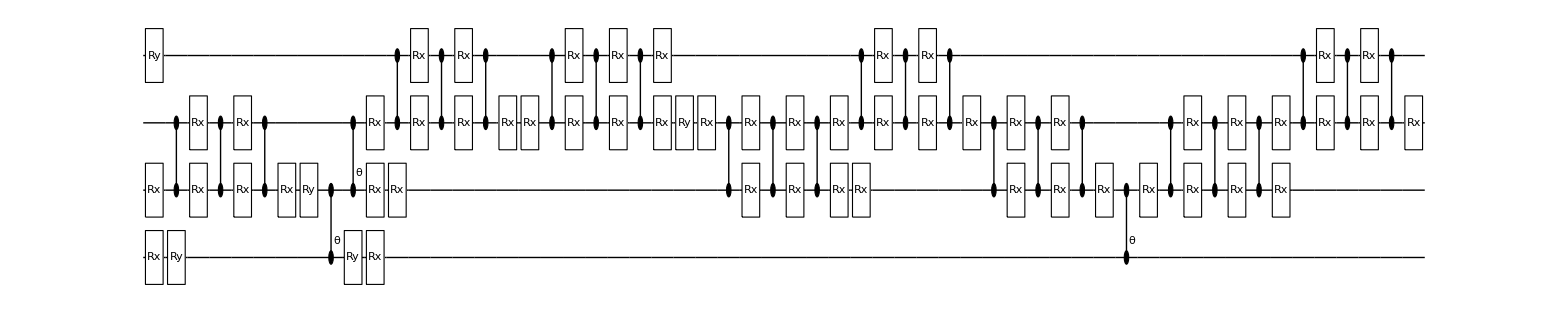
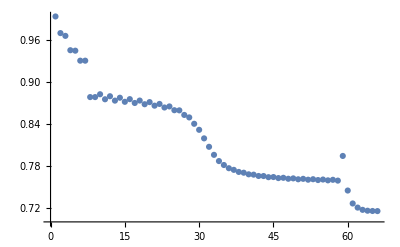
0.715163
822.611 min
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],Ry_0[θ_123],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14011,θ_9→-3.12787,θ_15→3.14151,θ_17→-3.14051,θ_33→-1.57077,θ_42→1.56811,θ_50→-0.785303,θ_56→-1.58094,θ_68→1.56753,θ_69→-1.57051,θ_103→0.392645,θ_120→-1.56017,θ_123→0.783353|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GCDSTO @Thu 27 Oct 2022 03:07:53

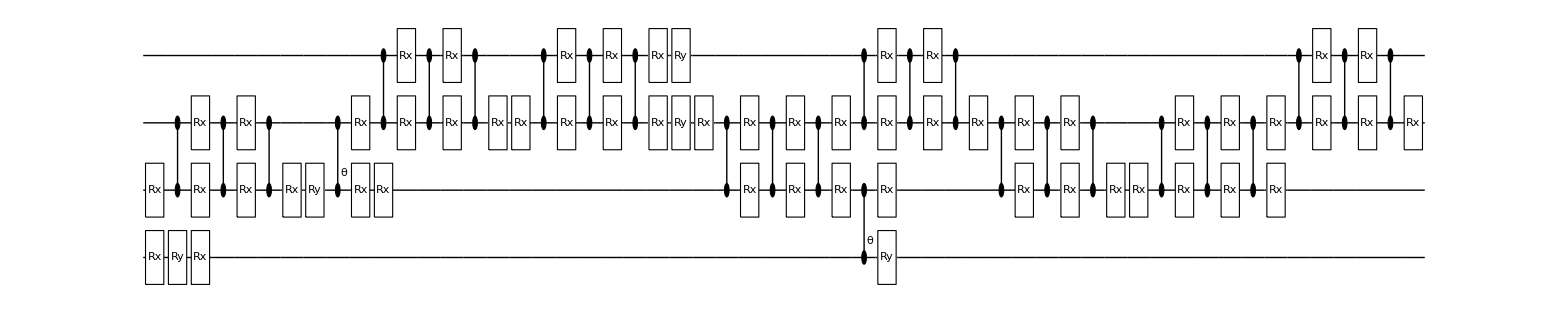
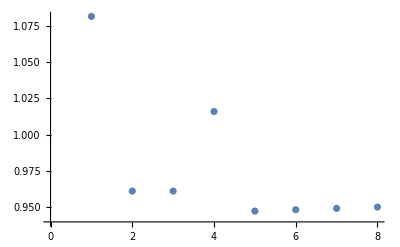
0.94718
139.062 min
-Graphics-
{Rx_0[θ_120],Rx_1[π/2],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],Rx_0[θ_17],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],C_0[Ph_1[θ_97]],Rx_2[π/2],Rx_3[π/2],Rx_1[π/2],Ry_0[θ_104],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14302,θ_9→-3.14044,θ_15→3.14485,θ_16→3.14356,θ_17→-3.13957,θ_33→-1.56828,θ_42→1.57209,θ_68→1.57409,θ_69→-1.56791,θ_97→1.56849,θ_104→1.5705,θ_120→-0.0115593|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GFD @Thu 27 Oct 2022 05:26:57

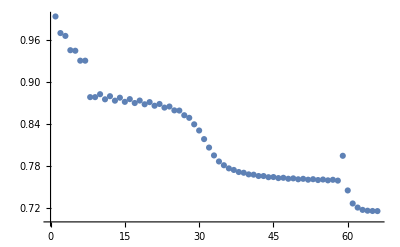
0.715117
467.761 min
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],Ry_0[θ_123],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14007,θ_9→-3.12786,θ_15→3.1415,θ_17→-3.14054,θ_33→-1.57077,θ_42→1.56811,θ_50→-0.785303,θ_56→-1.58094,θ_68→1.56753,θ_69→-1.57052,θ_103→0.392645,θ_120→-1.56016,θ_123→0.783341|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GFDSTO @Thu 27 Oct 2022 13:14:43

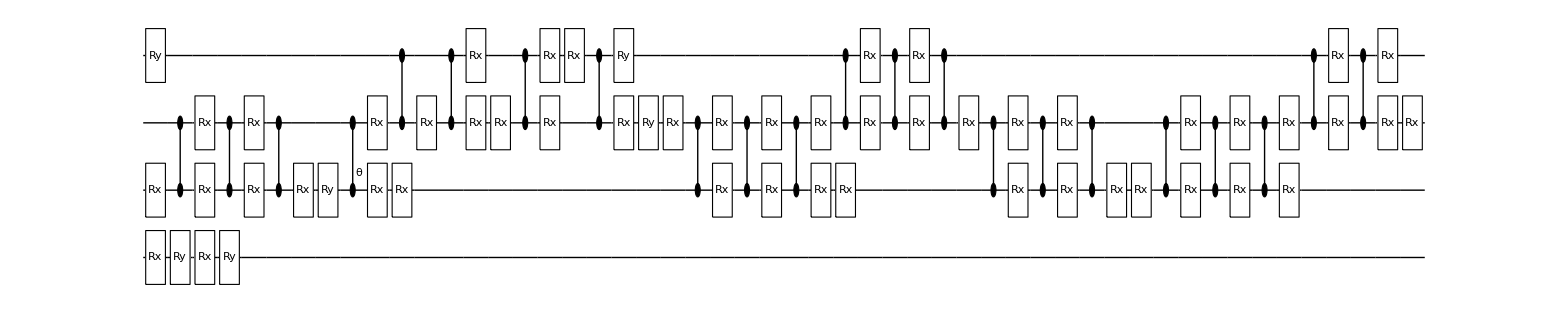
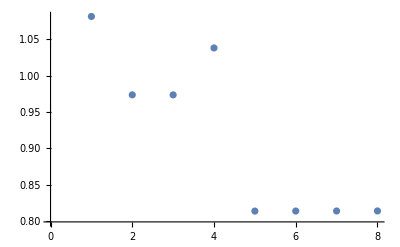
0.813576
61.7455 min
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],Rx_0[θ_17],C_1[Z_2],Ry_0[θ_104],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],Rx_2[π/2],C_2[Z_3],Rx_3[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Ry_3[θ_16],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],Rx_2[π/2]}
<|θ_7→3.1404,θ_9→-3.13532,θ_16→3.1499,θ_17→-3.14152,θ_33→-1.58802,θ_42→1.56632,θ_56→-1.56802,θ_68→1.56031,θ_69→-1.55793,θ_104→1.56839,θ_120→-0.0154094|>
-Graphics-

```mathematica
Table[
conf=confdef;
conf["ansatz"]=ansatz/.CustomGatesDefinitions;
conf["θvars"]=θvars;
  conf["grad"]=g;
res=CircuitSynthesis[4,conf];
results[g]=res;
,{g,grads}];
```

```mathematica
grads[[5;;]]
```

{GPSTO,GCD,GCDSTO,GFD,GFDSTO}

Compilation with predetermined ansatz using gradient methode GPSTO @Tue 25 Oct 2022 14:31:22

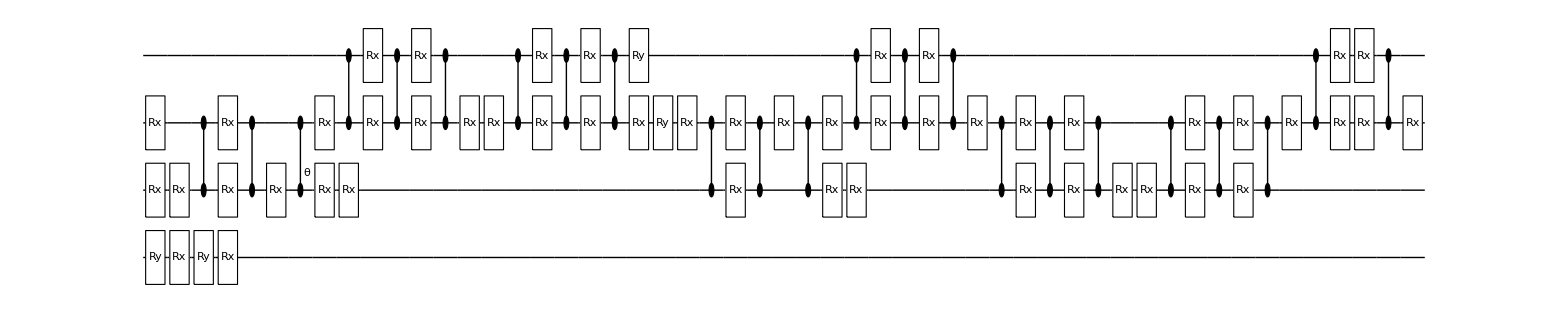
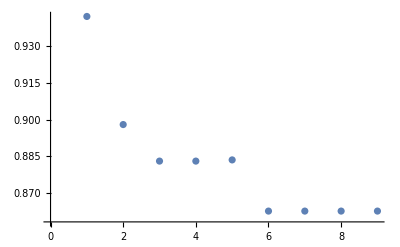
0.862595
152.54 min
-Graphics-
{Rx_1[π/2],Ry_0[θ_123],Rx_2[π/2],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Ry_0[θ_7],Rx_1[π/2],Rx_2[π/2],Rx_0[θ_17],C_1[Z_2],Rx_1[π/2],C_1[Ph_2[θ_33]],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Ry_3[θ_16],Ry_2[θ_68],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.12433,θ_9→-3.14348,θ_16→3.15191,θ_17→-3.12098,θ_33→-1.5653,θ_68→1.57081,θ_69→-1.55557,θ_123→0.787298,θ_124→1.55524|>
-Graphics-

Compilation with predetermined ansatz using gradient methode GCD @Tue 25 Oct 2022 17:03:54

```mathematica
Table[
conf=confdef;
conf["ansatz"]=ansatz/.CustomGatesDefinitions;
conf["θvars"]=θvars;
    conf["grad"]=g;
res=CircuitSynthesis[4,conf];
results[g]=res;
,{g,grads[[5;;]]}];
```

Compilation with predetermined ansatz using gradient methode NGAN @Mon 24 Oct 2022 03:25:14

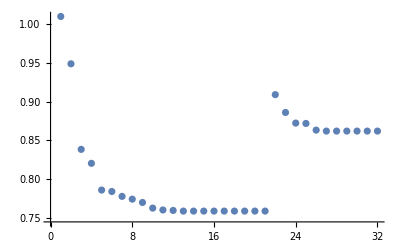
0.861879
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],C_0[Ph_1[θ_97]],Rx_2[π/2],Rx_3[π/2],Rx_1[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.55836,θ_9→-3.16855,θ_11→-5.56188,θ_15→3.21161,θ_16→3.15243,θ_17→-2.69493,θ_33→-1.49612,θ_42→1.58961,θ_50→-1.58227,θ_56→-1.57517,θ_59→1.49417,θ_68→1.49833,θ_69→-1.48895,θ_97→2.42026,θ_103→0.942932,θ_104→1.5754,θ_120→-1.56598,θ_123→1.28014,θ_124→1.08354|>
-Graphics-

{0.861879,{1.01004,0.94883,0.838235,0.820174,0.785648,0.783763,0.777467,0.773857,0.769593,0.762308,0.759894,0.759306,0.758451,0.758451,0.758454,0.758457,0.75846,0.758463,0.758466,0.758468,0.758471,0.90897,0.88593,0.872222,0.871729,0.863124,0.861879,0.861878,0.861878,0.861879,0.861879,0.861879},{Rx_0[θ_120],Ry_3[θ_56],Rx_1[π/2],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],Rx_1[θ_9],C_2[Z_3],Rx_1[π/2],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],C_0[Ph_1[θ_97]],Rx_2[π/2],Rx_3[π/2],Rx_1[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]},<|θ_7→3.55836,θ_9→-3.16855,θ_11→-5.56188,θ_15→3.21161,θ_16→3.15243,θ_17→-2.69493,θ_33→-1.49612,θ_42→1.58961,θ_50→-1.58227,θ_56→-1.57517,θ_59→1.49417,θ_68→1.49833,θ_69→-1.48895,θ_97→2.42026,θ_103→0.942932,θ_104→1.5754,θ_120→-1.56598,θ_123→1.28014,θ_124→1.08354|>,1515,{0,0,0,0}}

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz;
conf["θvars"]=θvars;
conf["grad"]="NGAN";
ngan=CircuitSynthesis[4,conf]
```

Compilation with predetermined ansatz using gradient methode NGSTO @Mon 24 Oct 2022 17:50:14

SANITY CHEK: cost=1.07733

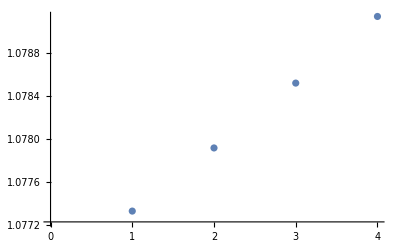
1.07733
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_1[θ_9],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_0[Ph_1[θ_97]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14156,θ_9→-3.14159,θ_11→-5.49778,θ_15→3.14159,θ_16→3.14159,θ_17→-3.14159,θ_33→-1.57079,θ_42→1.5708,θ_50→-0.785399,θ_56→-1.5708,θ_59→1.57079,θ_68→1.5708,θ_69→-1.5708,θ_97→1.5708,θ_103→0.392701,θ_104→1.57078,θ_120→-1.57076,θ_123→0.785398,θ_124→1.57076|>
-Graphics-

{1.07733,{1.07733,1.07792,1.07852,1.07914},{Rx_0[θ_120],Ry_3[θ_56],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_1[θ_9],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_0[Ph_1[θ_97]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]},<|θ_7→3.14156,θ_9→-3.14159,θ_11→-5.49778,θ_15→3.14159,θ_16→3.14159,θ_17→-3.14159,θ_33→-1.57079,θ_42→1.5708,θ_50→-0.785399,θ_56→-1.5708,θ_59→1.57079,θ_68→1.5708,θ_69→-1.5708,θ_97→1.5708,θ_103→0.392701,θ_104→1.57078,θ_120→-1.57076,θ_123→0.785398,θ_124→1.57076|>,4,{0,0,0,0}}

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz/.CustomGatesDefinitions;
conf["θvars"]=θvars;
conf["grad"]="NGSTO";
ngsto=CircuitSynthesis[4,conf]
```

```mathematica
HSDistance[noisycirc,ngsto[[4]],unitary,4]
```

0.999325

Compilation with predetermined ansatz using gradient methode GSTO @Mon 24 Oct 2022 17:52:49

SANITY CHEK: cost=1.03358

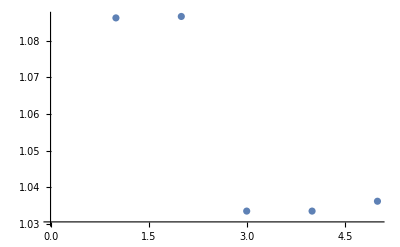
1.03358
-Graphics-
{Rx_0[θ_120],Ry_3[θ_56],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_1[θ_9],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_0[Ph_1[θ_97]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]}
<|θ_7→3.14108,θ_9→-3.1416,θ_11→-5.49818,θ_15→3.14191,θ_16→3.14182,θ_17→-3.1401,θ_33→-1.57095,θ_42→1.57066,θ_50→-0.78578,θ_56→-1.57047,θ_59→1.57112,θ_68→1.57057,θ_69→-1.57147,θ_97→1.57094,θ_103→0.392585,θ_104→1.57198,θ_120→-1.57275,θ_123→0.785774,θ_124→1.5698|>
-Graphics-

{1.03358,{1.08616,1.08655,1.03358,1.03358,1.03626},{Rx_0[θ_120],Ry_3[θ_56],Ry_0[θ_123],C_2[Ph_3[θ_59]],Rx_0[θ_124],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Ry_1[θ_42],C_0[Ph_1[θ_50]],Ry_0[θ_7],C_1[Ph_2[θ_33]],Rx_0[θ_17],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_1[θ_9],C_2[Ph_3[θ_11]],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[θ_15],Ry_2[θ_68],Ry_3[θ_16],Rx_2[θ_69],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],C_0[Ph_1[θ_97]],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],C_0[Ph_1[θ_103]],Ry_0[θ_104],Rx_1[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_1[Z_2],Rx_1[π/2],Rx_2[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2],Rx_3[π/2],C_2[Z_3],Rx_2[π/2]},<|θ_7→3.14108,θ_9→-3.1416,θ_11→-5.49818,θ_15→3.14191,θ_16→3.14182,θ_17→-3.1401,θ_33→-1.57095,θ_42→1.57066,θ_50→-0.78578,θ_56→-1.57047,θ_59→1.57112,θ_68→1.57057,θ_69→-1.57147,θ_97→1.57094,θ_103→0.392585,θ_104→1.57198,θ_120→-1.57275,θ_123→0.785774,θ_124→1.5698|>,5,{0,0,0,0}}

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz/.CustomGatesDefinitions;
conf["θvars"]=θvars;
conf["grad"]="GSTO";
gsto=CircuitSynthesis[4,conf]
```

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz;
conf["θvars"]=θvars;
conf["grad"]="GPS";
gps=CircuitSynthesis[4,conf]
```

Compilation with predetermined ansatz using gradient methode GPS @Mon 24 Oct 2022 17:54:20

$Aborted

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz/.CustomGatesDefinitions;
conf["θvars"]=θvars;
conf["grad"]="GPSTO";
gpsto=CircuitSynthesis[4,conf]
```

Compilation with predetermined ansatz using gradient methode GPSTO @Mon 24 Oct 2022 17:58:17

ApplyCircuit::error: Cannot simulate Deph_(1,2)[0.]. Probabilities must be in [0, 1]. The qureg (id 10) has been restored to its prior state.

General::stop: Further output of ApplyCircuit::error will be suppressed during this calculation.

$Aborted